## Dunaev Viktor 4 kurs 6 gruppa

## a)

```mathematica
a1 = 296454621;
c1 = 48840859;
M1 = 2^31;
β1 = Max[c1,M1-c1];
```

```mathematica
(*The multiplicative congruential method*)
(*base random variable*)
BRV1[a_] := Mod[β1*a,M1]
```

```mathematica
at = a1;
values1 = Table[at=(BRV1[at]);at/M1,2000]//N;
Print[# "th value: ", values1⟦#⟧//N] & [1]
Print[# "th value: ", values1⟦#⟧//N] & [15]
Print[# "th value: ", values1⟦#⟧//N] & [100]
Print[# "th value: ", values1⟦#⟧//N] & [900]
Print[# "th value: ", values1⟦#⟧//N] & [1000]
```

th value: 0.426003

15 th value: 0.810096

100 th value: 0.70094

900 th value: 0.53381

1000 th value: 0.0170195

## b)

```mathematica
a2 = 302711857;
c2 = 37330745;
M2 = 2^31;
K = 64;
β2 = Max[c2,M2-c2];
```

```mathematica
BRV2[a_] := Mod[β2*a,M2]
```

```mathematica
at = a2;
values2 = Table[at=(BRV2[at]);at/M2,2000]//N;
Print[# "th value: ", values2⟦#⟧//N] & [1]
Print[# "th value: ", values2⟦#⟧//N] & [15]
Print[# "th value: ", values2⟦#⟧//N] & [100]
Print[# "th value: ", values2⟦#⟧//N] & [900]
Print[# "th value: ", values2⟦#⟧//N] & [1000]
```

th value: 0.648701

15 th value: 0.681435

100 th value: 0.35606

900 th value: 0.372474

1000 th value: 0.764704

```mathematica
MMM[seq1_,seq2_] := (
s = 0;
valuesResult = Table[0,1000];
suppTable = Table[0,K];
For[i=1,i<=K,i++,
	suppTable⟦i⟧ = seq1⟦i⟧;
];
For[i=1,i<=1000,i++,
	s = IntegerPart[seq2⟦i⟧ * K]+1;
	valuesResult⟦i⟧ = suppTable⟦s⟧;
	suppTable⟦s⟧ = seq1⟦i+K⟧;
];
Print[# "th value: ", valuesResult⟦#⟧//N] & [1]
Print[# "th value: ", valuesResult⟦#⟧//N] & [15]
Print[# "th value: ", valuesResult⟦#⟧//N] & [100]
Print[# "th value: ", valuesResult⟦#⟧//N] & [900]
Print[# "th value: ", valuesResult⟦#⟧//N] & [1000]
)
```

```mathematica
MMM[values1,values2]
```

th value: 0.0593535

15 th value: 0.900636

100 th value: 0.981762

900 th value: 0.758502

1000 th value: 0.177526

Null^5

```mathematica
(* MomentsEqualityTest[seq_, delta_] := (
n = Length[seq];
m = (1/n)*Total[seq];
ss = (1/(n-1))Total[(seq-m)^2];
ξ1 = m - 0.5;
ξ2 = ss - 1/12;
c1 = Sqrt[12*n];
c2 = ((n-1)/n)*(0.0056 * n^(-1) + 0.0028 * n^(-2) - 0.0083n^(-3))^(-0.5);
h = (c1 * Abs[ξ1] < delta) && (c2 * Abs[ξ2] < delta);
If[h,
	Print["Good sequence!"],
	Print["Bad sequence!"]]
) *)
```

```mathematica
(* delta = 0.83^(-1);
MomentsEqualityTest[values1,delta] *)
```

## 5)

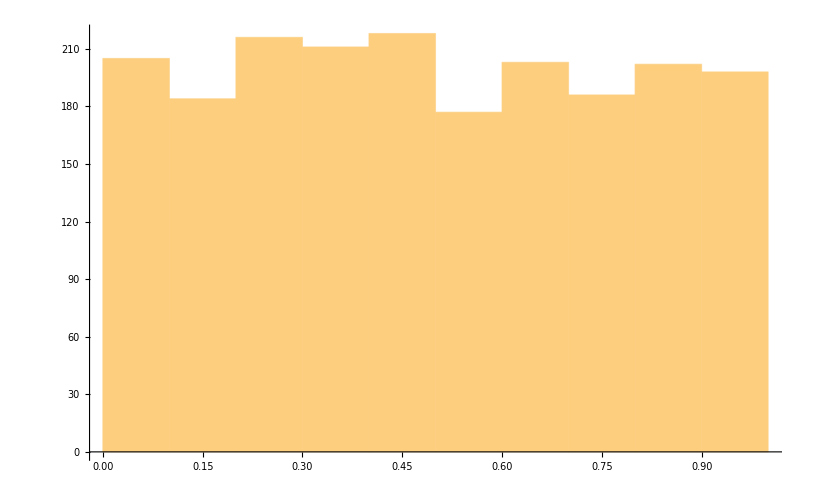

```mathematica
Histogram[values1]
```

## 4)

```mathematica
Correlation[values1,values2]
```

0.0151928